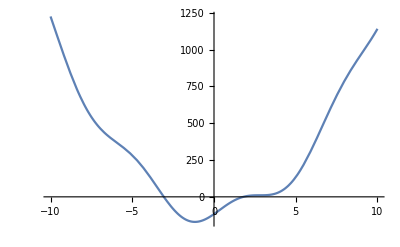

```mathematica
f[x_] := 13 x^2+77 Sin[x] - 117;
Plot[f[x],{x,-10,10}]
```

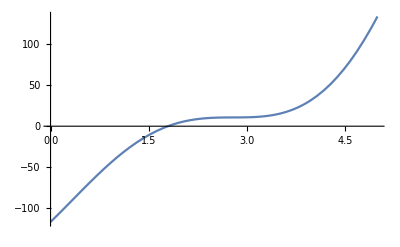

```mathematica
Plot[f[x],{x,0,5}]
```

```mathematica
(*broqt na korenite sa dva*)
```

```mathematica
(*lokalizirame nay-malkiq koren*)
```

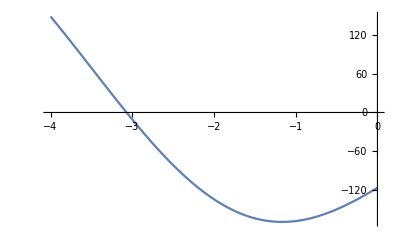

```mathematica
Plot[f[x],{x,-4,0}]
```

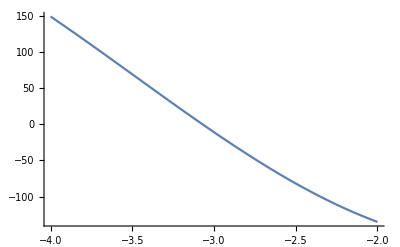

```mathematica
Plot[f[x],{x,-4,-2}]
```

```mathematica
f[-4.]
```

149.274

```mathematica
f[-2.]
```

-135.016

```mathematica
(*kraishtata na intervala znacite sa razlichni
f[-4.] = 149.274
f[-2.] = -135.016
	sledva che funkciqta ima pone edin koren
*)
```

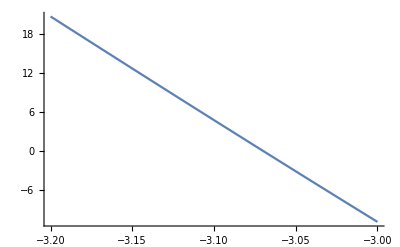

```mathematica
Plot[f[x],{x,-3.2,-3}]
```

```mathematica
f[-3.2]
```

20.6148

```mathematica
f[-3.]
```

-10.8662

```mathematica
(*kraishtata na intervala znacite sa razlichni
f[-3.2] = 20.614809043923685
f[-3.] = -10.866240620609773
	sledva che funkciqta ima pone edin koren
*)
```

```mathematica
(*proverka na usloviqta na metoda:*)
```

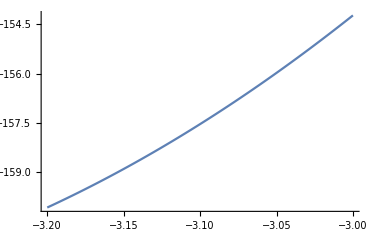

```mathematica
Plot[f'[x],{x,-3.2,-3}]
```

```mathematica
(*izvod: purvata proizvodna f'(x) v intervala [-3.2;-3] ima stoynosti mejdu -160 do -154*)
(*sledovatelno f'(x)<0 v razglejdaniq interval otgovarq na uslovieto che e s postoqnen znak*)
```

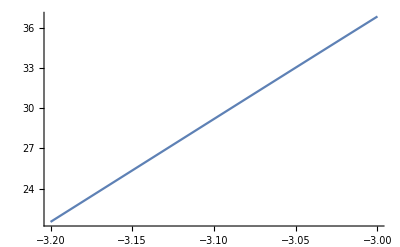

```mathematica
Plot[f''[x],{x,-3.2,-3}]
```

```mathematica
(*izvod: purvata proizvodna f'(x) v intervala [-3.2;-3] ima stoynosti mejdu 20 do 40*)
```

```mathematica
(*izbor na nachalno priblijenie i na postoqnna tochka f(x0).f''<0 *)
(*otgovarq na uslovieto che e s postoqnen znak*)
(*tochka na priblijenie izbirame kydeto e otricatelnata chast*)
(*postoqnnata tochka q izbirame da e drugiq kray*)
```

```mathematica
x0 = -3.;
p = -3.2;
```

```mathematica
f[x0]
```

-10.8662

```mathematica
f[p]
```

20.6148

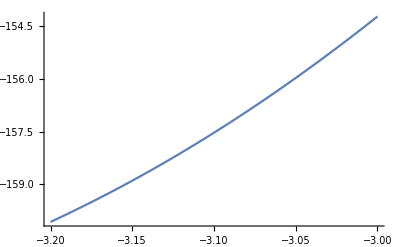

```mathematica
Plot[f'[x],{x,-3.2,-3}]
```

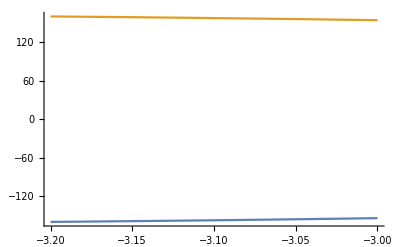

```mathematica
Plot[{f'[x],Abs[f'[x]]},{x,-3.2,-3}]
```

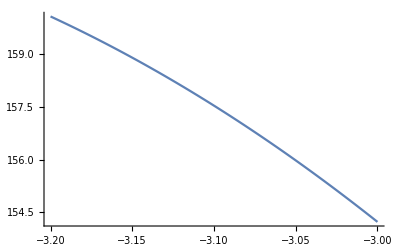

```mathematica
Plot[Abs[f'[x]],{x,-3.2,-3}]
```

```mathematica
(*m1 e minimalnata stoynost*)
```

```mathematica
m1 = Abs[f'[-3.]]
```

154.229

```mathematica
(*M1 e maksimalnata stoynost*)
```

```mathematica
M1 = Abs[f'[-3.2]]
```

160.069

```mathematica
CC = (M1 - m1)/m1
```

0.037861

```mathematica
(*zapochvame s iteraciite*)
```

```mathematica
x0 = -3.;
p = -3.2;
M1 = Abs[f'[-3.2]];
m1 = Abs[f'[-3.]];
xpred = x0;
CC = (M1 - m1)/m1;
Print["n=0: x= ",x0," f(x)= ",f[x0]];
For[n=0,n<= 15,n++,
xsled = xpred - f[xpred]/(f[xpred]-f[p])(xpred-p);
eps = CC* Abs[xsled - xpred];
Print["n=",n+1," : x=",SetPrecision[xsled,12]," f(x)=",f[xsled]," eps=",eps];
xpred = xsled;
]
```

n=0: x= -3. f(x)= 637.465

n=1 : x=-1.97278866766 f(x)=113.377 eps=0.0134415

n=2 : x=-1.75813659375 f(x)=43.7762 eps=0.00280881

n=3 : x=-1.67020264828 f(x)=19.9228 eps=0.00115065

n=4 : x=-1.62910841242 f(x)=9.70405 eps=0.000537736

n=5 : x=-1.6088337931 f(x)=4.8795 eps=0.000265302

n=6 : x=-1.5985733295 f(x)=2.49244 eps=0.000134263

n=7 : x=-1.59331510013 f(x)=1.2833 eps=0.0000688062

n=8 : x=-1.59060317879 f(x)=0.663447 eps=0.0000354866

n=9 : x=-1.58919993742 f(x)=0.343714 eps=0.000018362

n=10 : x=-1.58847262825 f(x)=0.178263 eps=9.51715×10^-6

n=11 : x=-1.58809533047 f(x)=0.0925058 eps=4.9371×10^-6

n=12 : x=-1.58789951563 f(x)=0.0480181 eps=2.56232×10^-6

n=13 : x=-1.58779786531 f(x)=0.0249291 eps=1.33014×10^-6

n=14 : x=-1.58774509073 f(x)=0.0129432 eps=6.90578×10^-7

n=15 : x=-1.58771768962 f(x)=0.00672042 eps=3.58555×10^-7

n=16 : x=-1.58770346222 f(x)=0.00348947 eps=1.86172×10^-7

```mathematica
(*sus stop kriteriy*)
x0 = -3.;
p = -3.2;
M1 = Abs[f'[-3.2]];
m1 = Abs[f'[-3.]];
xpred = x0;
CC = (M1 - m1)/m1;
Print["n=0: x= ",x0," f(x)= ",f[x0]];
epsusl = 10^(-5);
eps = 1;
For[n=0,eps >= epsusl,n++,
xsled = xpred - f[xpred]/(f[xpred]-f[p])(xpred-p);
eps = CC* Abs[xsled - xpred];
Print["n=",n+1," : x=",SetPrecision[xsled,12]," f(x)=",f[xsled]," eps=",eps];
xpred = xsled;
]
```

n=0: x= -3. f(x)= 637.465

n=1 : x=-1.97278866766 f(x)=113.377 eps=0.0134415

n=2 : x=-1.75813659375 f(x)=43.7762 eps=0.00280881

n=3 : x=-1.67020264828 f(x)=19.9228 eps=0.00115065

n=4 : x=-1.62910841242 f(x)=9.70405 eps=0.000537736

n=5 : x=-1.6088337931 f(x)=4.8795 eps=0.000265302

n=6 : x=-1.5985733295 f(x)=2.49244 eps=0.000134263

n=7 : x=-1.59331510013 f(x)=1.2833 eps=0.0000688062

n=8 : x=-1.59060317879 f(x)=0.663447 eps=0.0000354866

n=9 : x=-1.58919993742 f(x)=0.343714 eps=0.000018362

n=10 : x=-1.58847262825 f(x)=0.178263 eps=9.51715×10^-6